```mathematica
χ42=(√2 d42^2 Nat (-ⅈ (5 √7-2 √10) omegac1^2+8 √10 (γ21+ⅈ δ) (ⅈ γ32-δ+Δ)))/(5 e0 (omegac1^2 (2 ⅈ w43+7 γ32+2 γ42+9 ⅈ (δ-Δ))-8 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ)
χ32=-((d32^2 Nat ((-35+2 √70) omegac2^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ-Δ)))/(5 e0 (omegac2^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ-9 Δ)+8 (γ21+ⅈ δ) (γ32+ⅈ (δ-Δ)) (w43-ⅈ γ42+δ-Δ)) ℏ))
χ24=(d42^2 Nat (-ⅈ (4 √5-5 √14) omegac1^2-16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ)))/(5 e0 (-8 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ) (w43+ⅈ γ42+δ-Δ)+omegac1^2 (-2 ⅈ w43+7 γ32+2 γ42-9 ⅈ δ+9 ⅈ Δ)) ℏ)
χ23=(d32^2 Nat ((35 √2-4 √35) omegac2^2-40 √2 (ⅈ γ21+δ) (w43+ⅈ γ42+δ-Δ)))/(5 √2 e0 (omegac2^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ-9 Δ)+8 (γ21-ⅈ δ) (γ32-ⅈ (δ-Δ)) (w43+ⅈ γ42+δ-Δ)) ℏ)
```

(√2 d42^2 Nat (-ⅈ (5 √7-2 √10) omegac1^2+8 √10 (γ21+ⅈ δ) (ⅈ γ32-δ+Δ)))/(5 e0 (omegac1^2 (2 ⅈ w43+7 γ32+2 γ42+9 ⅈ (δ-Δ))-8 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ)

-(d32^2 Nat ((-35+2 √70) omegac2^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ-Δ)))/(5 e0 (omegac2^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ-9 Δ)+8 (γ21+ⅈ δ) (γ32+ⅈ (δ-Δ)) (w43-ⅈ γ42+δ-Δ)) ℏ)

(d42^2 Nat (-ⅈ (4 √5-5 √14) omegac1^2-16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ)))/(5 e0 (-8 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ) (w43+ⅈ γ42+δ-Δ)+omegac1^2 (-2 ⅈ w43+7 γ32+2 γ42-9 ⅈ δ+9 ⅈ Δ)) ℏ)

(d32^2 Nat ((35 √2-4 √35) omegac2^2-40 √2 (ⅈ γ21+δ) (w43+ⅈ γ42+δ-Δ)))/(5 √2 e0 (omegac2^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ-9 Δ)+8 (γ21-ⅈ δ) (γ32-ⅈ (δ-Δ)) (w43+ⅈ γ42+δ-Δ)) ℏ)

# Doppler Broadening of χ42

Error

```mathematica
cef[z_,n_]:=
(*
Program reproduced from "J.A.C.Wiedeman,Computation of the Complex Error Funcion",SIAM J Numer Anal 31 (5),1497-1518 (1994);
Computes the Faddeeva or plasma discharge function;
w(z)=exp(-z^2)erfc(-iz) using a rational series with;
N terms.It assumes that Im(z)>0 of Im(z)=0;
*)
Module[{M,M2,k,L,theta,t,f,a,Z,p,w},
M=2*n;M2=2*M;
k=Range[-M+1,M-1,1];(*M2=no.of sampling points*)
L=Sqrt[n/Sqrt[2]];(*Optimal choice of L *)
theta=k*Pi/M;t=L*Tan[theta/2];(*Variable theta and t*)
f=Prepend[Exp[-t^2]*(L^2+t^2),0];
a=Re[Fourier[RotateRight[f,Length[f]/2//Round],FourierParameters->{1, 1}]]/M2;(*Coefficients of transform*)
a=Reverse[a[[Range[2,n+1]]]];(*Reorder coefficients*)
Z=(L+I*z)/(L-I*z);
p=Sum[a[[i]] Z^(Length[a]-i),{i,1,Length[a]}];
(*Polynomial evaluation*)
w=2*p/(L-I*z)^2+(1/Sqrt[Pi])/(L-I*z);
w
]
```

Doppler Shift

```mathematica
int=I*(Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v -Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]/.{Log[α1]->-( ⅈ π+Log[-1/α1]),Log[α2]->-( ⅈ π+Log[-1/α2]),Erfi[α1/u]->Erfc[-I α1/u]-I,Erfi[α2/u]->Erfc[-I α2/u]-I}//FullSimplify)
```

(ⅈ π (ⅇ^(-α1^2/u^2) (Zα-α1) Erfc[-(ⅈ α1)/u]+ⅇ^(-α2^2/u^2) (-Zα+α2) Erfc[-(ⅈ α2)/u]))/(α1-α2)

```mathematica
(*Faster*)
int=(ⅈ π ((Zα-α1) cef[α1/u]+ (-Zα+α2)cef[α2/u]))/(α1-α2)
```

(ⅈ π ((Zα-α1) cef[α1/u]+(-Zα+α2) cef[α2/u]))/(α1-α2)

```mathematica
Clear[α1,α2,Zα,solα,solZα,demon,numer,cefD,cefN,v,γ21]
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
demon=Denominator[s42]/ ⅇ^(v^2/u^2);
numer=Numerator[s42];
cefD=CoefficientList[demon,v];
cefN=CoefficientList[numer,v];
solα=Solve[demon==0,v]//ExpandAll//FullSimplify;
solZα=Solve[numer==0,v]//ExpandAll//FullSimplify;
(*Constant, α1,α2,Zα*)
solα42={A->cefN[[-1]]/cefD[[-1]],α1-> solα[[1,1,2]],α2->solα[[2,1,2]],Zα->solZα[[1,1,2]]}//ExpandAll//FullSimplify;
```

```mathematica
Clear[α1,α2,Zα,solα,solZα,demon,numer,cefD,cefN]
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
demon=Denominator[s32]/ ⅇ^(v^2/u^2);
numer=Numerator[s32];
cefD=CoefficientList[demon,v];
cefN=CoefficientList[numer,v];
solα=Solve[demon==0,v]//ExpandAll//FullSimplify;
solZα=Solve[numer==0,v]//ExpandAll//FullSimplify;
(*Constant, α1,α2,Zα*)
solα32={A->cefN[[-1]]/cefD[[-1]],α1-> solα[[1,1,2]],α2->solα[[2,1,2]],Zα->solZα[[1,1,2]]}//ExpandAll//FullSimplify;
```

```mathematica
Clear[α1,α2,Zα,solα,solZα,demon,numer,cefD,cefN]
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
demon=Denominator[s24]/ ⅇ^(v^2/u^2);
numer=Numerator[s24];
cefD=CoefficientList[demon,v];
cefN=CoefficientList[numer,v];
solα=Solve[demon==0,v]//ExpandAll//FullSimplify;
solZα=Solve[numer==0,v]//ExpandAll//FullSimplify;
(*Constant, α1,α2,Zα*)
solα24={A->cefN[[-1]]/cefD[[-1]],α1-> solα[[1,1,2]],α2->solα[[2,1,2]],Zα->solZα[[1,1,2]]}//ExpandAll//FullSimplify;
```

```mathematica
Clear[α1,α2,Zα,solα,solZα,demon,numer,cefD,cefN]
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
demon=Denominator[s23]/ ⅇ^(v^2/u^2);
numer=Numerator[s23];
cefD=CoefficientList[demon,v];
cefN=CoefficientList[numer,v];
solα=Solve[demon==0,v]//ExpandAll//FullSimplify;
solZα=Solve[numer==0,v]//ExpandAll//FullSimplify;
(*Constant, α1,α2,Zα*)
solα23={A->cefN[[-1]]/cefD[[-1]],α1-> solα[[1,1,2]],α2->solα[[2,1,2]],Zα->solZα[[1,1,2]]}//ExpandAll//FullSimplify;
```

```mathematica
Hey42=A int/.solα42//ExpandAll//FullSimplify;
Hey23=A int/.solα23//ExpandAll//FullSimplify;
Hey24=A int/.solα24//ExpandAll//FullSimplify;
Hey32=A int/.solα32//ExpandAll//FullSimplify;
```

```mathematica
{Hey42,Hey32,Hey24,Hey23}//TableForm
```

(c d42^2 Nat √(π/5) ((-c wc ((5+√70) omegac1^2+8 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))) cef[(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc^2 (γ21+ⅈ δ))]+(c wc ((5+√70) omegac1^2+8 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))) cef[(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc^2 (γ21+ⅈ δ))]))/(e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)) ℏ)
(c d32^2 Nat √π ((ⅈ (-25+4 √70) omegac2^2+5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+40 (w43+ⅈ (γ32-γ42)) (γ21+ⅈ δ)) cef[(c (-9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ))]+(ⅈ (25-4 √70) omegac2^2+5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)-40 (w43+ⅈ (γ32-γ42)) (γ21+ⅈ δ)) cef[(c (-9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ))]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2) ℏ)
(c d42^2 Nat √(π/5) ((c wc ((5+√70) omegac1^2+8 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))) cef[(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc^2 (γ21-ⅈ δ))]+(c wc (-(5+√70) omegac1^2+8 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))) cef[(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc^2 (γ21-ⅈ δ))]))/(e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)) ℏ)
(c d32^2 Nat √(π/2) ((ⅈ (25 √2-8 √35) omegac2^2+5 √2 (ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (w43-ⅈ (γ32-γ42)) (γ21-ⅈ δ))) cef[(c (9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ))]+(-ⅈ (25 √2-8 √35) omegac2^2+5 √2 (ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)-8 (w43-ⅈ (γ32-γ42)) (γ21-ⅈ δ))) cef[(c (9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ))]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2) ℏ)

```mathematica
{solα42,solα32,solα24,solα23}[[All,1]]//TableForm
{solα42,solα32,solα24,solα23}[[All,{2,3}]]//TableForm
{solα42,solα32,solα24,solα23}[[All,4]]//TableForm
```

A→-(2 c d42^2 Nat)/(e0 √(5 π) u wc ℏ)
A→-(c d32^2 Nat)/(e0 √π u wc ℏ)
A→-(2 c d42^2 Nat)/(e0 √(5 π) u wc ℏ)
A→-(c d32^2 Nat)/(e0 √π u wc ℏ)

α1→(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 wc^2 (γ21+ⅈ δ)) | α2→(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 wc^2 (γ21+ⅈ δ))
α1→(c (-9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 wc (γ21+ⅈ δ)) | α2→(c (-9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 wc (γ21+ⅈ δ))
α1→(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 wc^2 (γ21-ⅈ δ)) | α2→(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 wc^2 (γ21-ⅈ δ))
α1→(c (9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 wc (γ21-ⅈ δ)) | α2→(c (9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 wc (γ21-ⅈ δ))

Zα→(c (-ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ)))/(16 √5 wc (γ21+ⅈ δ))
Zα→(c ((-35+2 √70) omegac2^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ-Δ)))/(40 wc (-ⅈ γ21+δ))
Zα→(c (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ)))/(16 √5 wc (γ21-ⅈ δ))
Zα→(c (ⅈ (35 √2-4 √35) omegac2^2+40 √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ-Δ)))/(40 √2 wc (γ21-ⅈ δ))

# Plot

Error

```mathematica
cef[z_,n_]:=
(*
Program reproduced from "J.A.C.Wiedeman,Computation of the Complex Error Funcion",SIAM J Numer Anal 31 (5),1497-1518 (1994);
Computes the Faddeeva or plasma discharge function;
w(z)=exp(-z^2)erfc(-iz) using a rational series with;
N terms.It assumes that Im(z)>0 of Im(z)=0;
*)
Module[{M,M2,k,L,theta,t,f,a,Z,p,w},
M=2*n;M2=2*M;
k=Range[-M+1,M-1,1];(*M2=no.of sampling points*)
L=Sqrt[n/Sqrt[2]];(*Optimal choice of L *)
theta=k*Pi/M;t=L*Tan[theta/2];(*Variable theta and t*)
f=Prepend[Exp[-t^2]*(L^2+t^2),0];
a=Re[Fourier[RotateRight[f,Length[f]/2//Round],FourierParameters->{1, 1}]]/M2;(*Coefficients of transform*)
a=Reverse[a[[Range[2,n+1]]]];(*Reorder coefficients*)
Z=(L+I*z)/(L-I*z);
p=Sum[a[[i]] Z^(Length[a]-i),{i,1,Length[a]}];
(*Polynomial evaluation*)
w=2*p/(L-I*z)^2+(1/Sqrt[Pi])/(L-I*z);
w
]
```

RBpress

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=794.76728224*10^-9;(*Transition frequency for 85Rb D1 line*)
dopp=2Pi/w0*Sqrt[2k*T1/MRb];
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

FUNCTION

```mathematica
Eitw0[T_,P_,diam_,γ21_,δ_,d_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43d,Δ,d32,d42,γ42,wp},

Δ=2Pi d*10^9;(*Raman detuning*)
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;


omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);


χ42=(√2 d42^2 Nat (-ⅈ (5 √7-2 √10) omegac1^2+8 √10 (γ21+ⅈ δ) (ⅈ γ32-δ+Δ)))/(5 e0 (omegac1^2 (2 ⅈ w43+7 γ32+2 γ42+9 ⅈ (δ-Δ))-8 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac2^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ-Δ)))/(5 e0 (omegac2^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ-9 Δ)+8 (γ21+ⅈ δ) (γ32+ⅈ (δ-Δ)) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ24=(d42^2 Nat (-ⅈ (4 √5-5 √14) omegac1^2-16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ)))/(5 e0 (-8 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ) (w43+ⅈ γ42+δ-Δ)+omegac1^2 (-2 ⅈ w43+7 γ32+2 γ42-9 ⅈ δ+9 ⅈ Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac2^2-40 √2 (ⅈ γ21+δ) (w43+ⅈ γ42+δ-Δ)))/(5 √2 e0 (omegac2^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ-9 Δ)+8 (γ21-ⅈ δ) (γ32-ⅈ (δ-Δ)) (w43+ⅈ γ42+δ-Δ)) ℏ);

{Exp[-2Pi*0.0254/(2wp)Im[ χ42]],Exp[-2Pi*0.0254/(2wp)Im[ χ32]],Exp[-2Pi*0.0254/(2wp)Im[ χ24]],Exp[-2Pi*0.0254/(2wp)Im[ χ23]]}
(*{Exp[-2Pi*0.0254/(2wp)Re[ χ42]],Exp[-2Pi*0.0254/(2wp)Re[ χ32]],Exp[-2Pi*0.0254/(2wp)Re[ χ24]],Exp[-2Pi*0.0254/(2wp)Re[ χ23]]}*)
]
```

```mathematica
Eit[T_,P_,diam_,gam_,δ_,d_,w43_] :=
Module[{Nat,Δ,γ21,γ32,γ42,d32,d42,ℏ,e0,c,wcn,u,wc,omegac1,omegac2,χ42,χ32,χ23,χ24},

Δ=2Pi d*10^9;(*Raman detuning*)

Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
(*w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;*)
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);

χ42=  (c d42^2 Nat √(π/5) ((-c wc ((5+√70) omegac1^2+8 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))) cef[1/(16 u wc^2 (γ21+ⅈ δ))(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ))))),50]+(c wc ((5+√70) omegac1^2+8 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))) cef[1/(16 u wc^2 (γ21+ⅈ δ))(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ))))),50]))/(e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)) ℏ);
χ32= (c d32^2 Nat √π ((ⅈ (-25+4 √70) omegac2^2+5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+40 (w43+ⅈ (γ32-γ42)) (γ21+ⅈ δ)) cef[(c (-9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ)),50]+(ⅈ (25-4 √70) omegac2^2+5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)-40 (w43+ⅈ (γ32-γ42)) (γ21+ⅈ δ)) cef[(c (-9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ)),50]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2) ℏ);

χ24=(c d42^2 Nat √(π/5) ((c wc ((5+√70) omegac1^2+8 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))) cef[1/(16 u wc^2 (γ21-ⅈ δ))(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ))),50]+(c wc (-(5+√70) omegac1^2+8 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ))+ⅈ √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))) cef[1/(16 u wc^2 (γ21-ⅈ δ))(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ))),50]))/(e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)) ℏ);
χ23=(c d32^2 Nat √(π/2) ((ⅈ (25 √2-8 √35) omegac2^2+5 √2 (ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (w43-ⅈ (γ32-γ42)) (γ21-ⅈ δ))) cef[(c (9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ)),50]+(-ⅈ (25 √2-8 √35) omegac2^2+5 √2 (ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)-8 (w43-ⅈ (γ32-γ42)) (γ21-ⅈ δ))) cef[(c (9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ γ32+ⅈ γ42)^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ)),50]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2) ℏ);

Exp[-2Pi*0.0254/(2 wcn)Im[(* χ42+χ32*)χ23+χ24]]
(*{Exp[-2Pi*0.0254/(2 wcn)Im[ χ42]],Exp[-2Pi*0.0254/(2wcn)Im[ χ32]],Exp[-2Pi*0.0254/(2wcn)Im[ χ24]],Exp[-2Pi*0.0254/(2wcn)Im[ χ23]]}*)
(*{Exp[-2Pi*0.0254/(2wcn)Re[ χ42]],Exp[-2Pi*0.0254/(2wcn)Re[ χ32]],Exp[-2Pi*0.0254/(2wcn)Re[ χ24]],Exp[-2Pi*0.0254/(2wcn)Re[ χ23]]}*)
]
```

```mathematica
Eitw0sc[T_,P_,diam_,γ21_,Δ_,d_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43d,δ,d32,d42,γ42,wp},

δ=Δ-2Pi (d)*10^9;
Nat=Rbpress[T][[1]];
wp=(794.76728224*10^-9);
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;


omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);




χ42=(√2 d42^2 Nat (-ⅈ (5 √7-2 √10) omegac1^2+8 √10 (γ21+ⅈ δ) (ⅈ γ32-δ+Δ)))/(5 e0 (omegac1^2 (2 ⅈ w43+7 γ32+2 γ42+9 ⅈ (δ-Δ))-8 (γ21+ⅈ δ) (-ⅈ γ32+δ-Δ) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac2^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ-Δ)))/(5 e0 (omegac2^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ-9 Δ)+8 (γ21+ⅈ δ) (γ32+ⅈ (δ-Δ)) (w43-ⅈ γ42+δ-Δ)) ℏ);
χ24=(d42^2 Nat (-ⅈ (4 √5-5 √14) omegac1^2-16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ)))/(5 e0 (-8 (γ21-ⅈ δ) (ⅈ γ32+δ-Δ) (w43+ⅈ γ42+δ-Δ)+omegac1^2 (-2 ⅈ w43+7 γ32+2 γ42-9 ⅈ δ+9 ⅈ Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac2^2-40 √2 (ⅈ γ21+δ) (w43+ⅈ γ42+δ-Δ)))/(5 √2 e0 (omegac2^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ-9 Δ)+8 (γ21-ⅈ δ) (γ32-ⅈ (δ-Δ)) (w43+ⅈ γ42+δ-Δ)) ℏ);

{Exp[-2Pi*0.0254/(2wp)Im[ χ42]],Exp[-2Pi*0.0254/(2wp)Im[ χ32]],Exp[-2Pi*0.0254/(2wp)Im[ χ24]],Exp[-2Pi*0.0254/(2wp)Im[ χ23]]}
(*{Exp[-2Pi*0.0254/(2wp)Re[ χ42]],Exp[-2Pi*0.0254/(2wp)Re[ χ32]],Exp[-2Pi*0.0254/(2wp)Re[ χ24]],Exp[-2Pi*0.0254/(2wp)Re[ χ23]]}*)
]
```

```mathematica
Eitsc[T_,P_,diam_,gam_,Δ_,d_,w43_] :=
Module[{Nat,δ,γ21,γ32,γ42,d32,d42,ℏ,e0,c,wcn,u,wc,omegac1,omegac2,χ42,χ32,χ23,χ24},

δ=Δ-2Pi (d)*10^9;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
(*w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;*)
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);
χ42=  (ⅈ c d42^2 Nat √(π/5) (5 (5 ⅈ c omegac1^2 wc+ⅈ √70 c omegac1^2 wc-8 c w43 wc γ21-8 ⅈ c wc γ21 γ32+8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))-8 ⅈ c w43 wc δ+8 c wc γ32 δ-8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21+ⅈ δ))(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ))))),50]+5 (-5 ⅈ c omegac1^2 wc-ⅈ √70 c omegac1^2 wc+8 c w43 wc γ21+8 ⅈ c wc γ21 γ32-8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+8 ⅈ c w43 wc δ-8 c wc γ32 δ+8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21+ⅈ δ))(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ))))),50]))/(5 e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)) ℏ);
χ32= -((c d32^2 Nat √π (-(-25 ⅈ omegac2^2+4 ⅈ √70 omegac2^2+40 w43 γ21+40 ⅈ γ21 γ32-40 ⅈ γ21 γ42+5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+40 ⅈ w43 δ-40 γ32 δ+40 γ42 δ) cef[(c (-9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ)),50]+(-25 ⅈ omegac2^2+4 ⅈ √70 omegac2^2+40 w43 γ21+40 ⅈ γ21 γ32-40 ⅈ γ21 γ42-5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+40 ⅈ w43 δ-40 γ32 δ+40 γ42 δ) cef[(c (-9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ)),50]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2) ℏ));

χ24=(ⅈ c d42^2 Nat √(π/5) (5 (-5 ⅈ c omegac1^2 wc-ⅈ √70 c omegac1^2 wc-8 c w43 wc γ21+8 ⅈ c wc γ21 γ32-8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))+8 ⅈ c w43 wc δ+8 c wc γ32 δ-8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21-ⅈ δ))(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ))),50]+5 (5 ⅈ c omegac1^2 wc+ⅈ √70 c omegac1^2 wc+8 c w43 wc γ21-8 ⅈ c wc γ21 γ32+8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))-8 ⅈ c w43 wc δ-8 c wc γ32 δ+8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21-ⅈ δ))(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ))),50]))/(5 e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)) ℏ);
χ23=-((ⅈ c d32^2 Nat √π ((-25 omegac2^2+4 √70 omegac2^2+40 ⅈ w43 γ21+40 γ21 γ32-40 γ21 γ42-5 √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+40 w43 δ-40 ⅈ γ32 δ+40 ⅈ γ42 δ) cef[(c (9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ)),50]-(-25 omegac2^2+4 √70 omegac2^2+40 ⅈ w43 γ21+40 γ21 γ32-40 γ21 γ42+5 √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+40 w43 δ-40 ⅈ γ32 δ+40 ⅈ γ42 δ) cef[(c (9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ)),50]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2) ℏ));
Exp[-2Pi*0.0254/(2wcn)Im[ (*χ42+χ32*)(χ23+χ24)]]
(*{Exp[-2Pi*0.0254/(2wcn)Im[ χ42]],Exp[-2Pi*0.0254/(2wcn)Im[ χ32]],Exp[-2Pi*0.0254/(2wcn)Im[ χ24]],Exp[-2Pi*0.0254/(2wcn)Im[ χ23]]}*)
(*{Exp[-2Pi*0.0254/(2wcn)Re[ χ42]],Exp[-2Pi*0.0254/(2wcn)Re[ χ32]],Exp[-2Pi*0.0254/(2wcn)Re[ χ24]],Exp[-2Pi*0.0254/(2wcn)Re[ χ23]]}*)
]
```

```mathematica
Eitsc1[T_,P_,diam_,gam_,Δ_,d_,w43_] :=
Module[{Nat,δ,γ21,γ32,γ42,d32,d42,ℏ,e0,c,wcn,u,wc,omegac1,omegac2,χ42,χ32,χ23,χ24},

δ=Δ-2Pi (d)*10^9;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
(*w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;*)
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d42*Sqrt[P/(Pi*(diam/2)^2)]);
χ42=  (ⅈ c d42^2 Nat √(π/5) (5 (5 ⅈ c omegac1^2 wc+ⅈ √70 c omegac1^2 wc-8 c w43 wc γ21-8 ⅈ c wc γ21 γ32+8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))-8 ⅈ c w43 wc δ+8 c wc γ32 δ-8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21+ⅈ δ))(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ))))),50]+5 (-5 ⅈ c omegac1^2 wc-ⅈ √70 c omegac1^2 wc+8 c w43 wc γ21+8 ⅈ c wc γ21 γ32-8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+8 ⅈ c w43 wc δ-8 c wc γ32 δ+8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21+ⅈ δ))(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2))+c wc (-9 ⅈ omegac1^2+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ))))),50]))/(5 e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (-ⅈ w43+γ32-γ42) (γ21+ⅈ δ)+64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)) ℏ);
χ32= -((c d32^2 Nat √π (-(-25 ⅈ omegac2^2+4 ⅈ √70 omegac2^2+40 w43 γ21+40 ⅈ γ21 γ32-40 ⅈ γ21 γ42+5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+40 ⅈ w43 δ-40 γ32 δ+40 γ42 δ) cef[(c (-9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ)),50]+(-25 ⅈ omegac2^2+4 ⅈ √70 omegac2^2+40 w43 γ21+40 ⅈ γ21 γ32-40 ⅈ γ21 γ42-5 ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+40 ⅈ w43 δ-40 γ32 δ+40 γ42 δ) cef[(c (-9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2)+8 (γ21+ⅈ δ) (w43-ⅈ (γ32+γ42+2 ⅈ (δ-Δ)))))/(16 u wc (γ21+ⅈ δ)),50]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (ⅈ w43-γ32+γ42) (γ21+ⅈ δ)-64 (w43+ⅈ (γ32-γ42))^2 (γ21+ⅈ δ)^2) ℏ));

χ24=(ⅈ c d42^2 Nat √(π/5) (5 (-5 ⅈ c omegac1^2 wc-ⅈ √70 c omegac1^2 wc-8 c w43 wc γ21+8 ⅈ c wc γ21 γ32-8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))+8 ⅈ c w43 wc δ+8 c wc γ32 δ-8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21-ⅈ δ))(-√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ))),50]+5 (5 ⅈ c omegac1^2 wc+ⅈ √70 c omegac1^2 wc+8 c w43 wc γ21-8 ⅈ c wc γ21 γ32+8 ⅈ c wc γ21 γ42+√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))-8 ⅈ c w43 wc δ-8 c wc γ32 δ+8 c wc γ42 δ) cef[1/(16 u wc^2 (γ21-ⅈ δ))(√(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2))+c wc (9 ⅈ omegac1^2+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ))),50]))/(5 e0 u wc √(c^2 wc^2 (-81 omegac1^4+80 omegac1^2 (ⅈ w43+γ32-γ42) (γ21-ⅈ δ)+64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)) ℏ);
χ23=-((ⅈ c d32^2 Nat √π ((-25 omegac2^2+4 √70 omegac2^2+40 ⅈ w43 γ21+40 γ21 γ32-40 γ21 γ42-5 √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+40 w43 δ-40 ⅈ γ32 δ+40 ⅈ γ42 δ) cef[(c (9 ⅈ omegac2^2-ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ)),50]-(-25 omegac2^2+4 √70 omegac2^2+40 ⅈ w43 γ21+40 γ21 γ32-40 γ21 γ42+5 √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+40 w43 δ-40 ⅈ γ32 δ+40 ⅈ γ42 δ) cef[(c (9 ⅈ omegac2^2+ⅈ √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2)+8 (γ21-ⅈ δ) (w43+ⅈ γ32+ⅈ γ42+2 δ-2 Δ)))/(16 u wc (γ21-ⅈ δ)),50]))/(10 e0 u wc √(81 omegac2^4+80 omegac2^2 (-ⅈ w43-γ32+γ42) (γ21-ⅈ δ)-64 (w43-ⅈ (γ32-γ42))^2 (γ21-ⅈ δ)^2) ℏ));
Exp[-2Pi*0.0254/(2wcn)Im[ χ42+χ32(*(χ23+χ24)*)]]
(*{Exp[-2Pi*0.0254/(2wcn)Im[ χ42]],Exp[-2Pi*0.0254/(2wcn)Im[ χ32]],Exp[-2Pi*0.0254/(2wcn)Im[ χ24]],Exp[-2Pi*0.0254/(2wcn)Im[ χ23]]}*)
(*{Exp[-2Pi*0.0254/(2wcn)Re[ χ42]],Exp[-2Pi*0.0254/(2wcn)Re[ χ32]],Exp[-2Pi*0.0254/(2wcn)Re[ χ24]],Exp[-2Pi*0.0254/(2wcn)Re[ χ23]]}*)
]
```

```mathematica
h
```

# Present

```mathematica
Manipulate[
Plot[
Evaluate[
Flatten[{Eitw0sc[T,P/1000,1.4/1000,γ*10^6 ,2Pi Δ*10^6,d,2Pi*w43*10^6],
Eitsc[T,P/1000,1.4/1000,γ*10^6 ,2Pi Δ*10^6,d,2Pi*w43*10^6]}]
]
,{d,-2,2},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed},{Brown,Dashed},Red,Blue,Black,Brown},PlotRange->{-1,10},Frame->True,Axes->False,PlotLegends->{"χ42","χ32","χ24","χ23","χ42","χ32","χ24","χ23"},ImageSize->800,FrameLabel-> {"ν-ν_o (GHz) ","transmission"}],
Style["Thoery",12,Bold],{{T,60,"T (C)"},0,80},{{P,200,"P(mW)"},0,1000},{{γ,1.5,"γ(MHz)"},0,1},{{ Δ,-800,"δ(MHz)"},-1000,1000,0.001},{{w43,360},-3000,3000},{sep,-0.5,0.5},Row[{Control[{{aa1,True,"χ42"},{True,False}}],Control[{{aa2,True,"χ32"},{True,False}}],Control[{{aa3,True,"χ24"},{True,False}}],Control[{{aa4,True,"χ23"},{True,False}}]
},Spacer[20]]]
```

```mathematica
Manipulate[
Show[
Plot[
Evaluate[
Flatten[{Eitw0[T,P/1000,1.4/1000,γ*10^6 ,2Pi  (δ+2(i-12))*10^6,d-sep,2Pi*w43*10^6],
Eit[T,P/1000,1.4/1000,γ*10^6 ,2Pi (δ+2(i-12))*10^6,d-sep,2Pi*w43*10^6]}]
]
,{d,-3,2},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed},{Brown,Dashed},Red,Blue,Black,Brown},PlotRange->{{-3.1,0},{0,3}},Frame->True,Axes->False,PlotLegends->{"χ42","χ32","χ24","χ23","χ42","χ32","χ24","χ23"},ImageSize->800,FrameLabel-> {"ν-ν_o (GHz) ","transmission"}]
,ListPlot[data200m[[i]]]],
Style["Thoery",12,Bold],{{T,44.4,"T (C)"},0,80},{{P,148,"P(mW)"},0,1000},{{γ,2,"γ(MHz)"},0,2},{{δ,-11.11,"δ(MHz)"},-20,20,0.001},{{w43,360},-3000,3000},{sep,-1.47,0.5},Row[{Control[{{aa1,True,"χ42"},{True,False}}],Control[{{aa2,True,"χ32"},{True,False}}],Control[{{aa3,True,"χ24"},{True,False}}],Control[{{aa4,True,"χ23"},{True,False}}]
},Spacer[20]],{{i,11},1,Length[data200m],1}]
```

Part::partd: Part specification data200m⟦1⟧ is longer than depth of object.

ListPlot::lpn: data200m⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[data200m⟦1⟧]].

Part::partd: Part specification data200m⟦1⟧ is longer than depth of object.

ListPlot::lpn: data200m⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[data200m⟦1⟧]].

Part::partd: Part specification data200m⟦1⟧ is longer than depth of object.

ListPlot::lpn: data200m⟦1⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[data200m⟦1⟧]].

```mathematica
Manipulate[
Plot3D[
Evaluate[Eitsc[T,P/1000,1.4/1000,γ*10^6 ,2Pi Δ*10^9,d,2Pi*w43*10^6]],
{d,-2,2},{Δ,-1,1}
,PlotRange->{-0.1,2},Axes->False,ImageSize->800,AxesLabel-> {"ν-ν_o (GHz) ","Δ(GHz)","transmission"},PlotPoints-> 50]
,
{{T,60,"T (C)"},0,80},{{P,200,"P(mW)"},0,1000},{{γ,1.5,"γ(MHz)"},0,1},{{w43,360},-3000,3000}
]
```

```mathematica
Manipulate[ListPlot[data200m[[i]],options],{i,1,Length[data200m],1}]
```

```mathematica
img=ListPlot3D[
Partition[Flatten[
Table[
Table[Flatten[{i,data200m[[i]][[j]]}],{j,1,Length[data200m[[i]]]}]
,{i,1,Length[data200m]}]
],3]
]
```

-Graphics3D-

```mathematica
img2=ListContourPlot[
Partition[Flatten[
Table[
Table[Flatten[{i,data200m[[i]][[j]]}],{j,1,Length[data200m[[i]]]}]
,{i,1,Length[data200m]}]
],3]
]
```

-Graphics-

```mathematica
Manipulate[
GraphicsRow[{Plot3D[
Evaluate[Eit[T,P/1000,1.4/1000,γ*10^6 ,2Pi (δ)*10^9,d,2Pi*w43*10^6]]
,{δ,-0.02,0.025},{d,-1.5,1.5}
,PlotRange->{-0.4,1},Axes->False,ImageSize->800,AxesLabel-> {"ν-ν_o (GHz) ","Δ(GHz)","transmission"},PlotPoints-> 20,Exclusions->None,ImageSize->700],
img
},ImageSize->1020]
,
{{T,60,"T (C)"},0,80},{{P,200,"P(mW)"},0,1000},{{γ,2,"γ(MHz)"},0,1},{{w43,360},-3000,3000}
]
```

```mathematica
Manipulate[
GraphicsRow[{img2,
ContourPlot[
Evaluate[Eit[T,P/1000,1.4/1000,γ*10^6 ,2Pi (δ)*10^9,d,2Pi*w43*10^6]]
,{δ,-0.02,0.025},{d,-1.5,1.5}
,PlotRange->{-0.1,2},Axes->False,ImageSize->500,AxesLabel-> {"ν-ν_o (GHz) ","Δ(GHz)","transmission"},PlotPoints-> 50,Contours->10,Exclusions->None]}]
,
{{T,60,"T (C)"},0,80},{{P,200,"P(mW)"},0,1000},{{γ,2,"γ(MHz)"},0,1},{{w43,360},-3000,3000}
]
```

# DAtacall

# Module

Cutting off the data

```mathematica
cutoff[list_]:=
Module[{hello1,hello2,pos1,pos2,temp},
temp=list[[5]];
pos1=Position[temp,Max[temp]][[1,1]];
pos2=Position[temp,Min[temp]][[1,1]];
Table[Reverse[Take[list[[k]],{pos1,pos2}]],{k,1,4}]
]
```

Normalizing the Data using Gaussian Filter

```mathematica
GF[data_,l_]:=Module[{smoothData,s,fit,f},
smoothData=GaussianFilter[data,4l];s=Flatten[DeleteCases[Reap[If[Total@Abs@Differences[smoothData[[#;;#+l]]]<0.0002,Sow[{#,smoothData[[#]]}]]&/@Range[1,Length[smoothData]-l]][[2]],Null],1];fit=LinearModelFit[s,{1,x},x];
f[x_]:=Evaluate[fit["BestFit"]];
Table[data[[x]]/f[x],{x,1,Length[data]}]
]
```

Xaxis

```mathematica
xaxisD[list1_,dd_:0]:=Module[{points,npoints,λSF3,λSF3PF2,λSF3PF3,ans,i,list},
list={Take[list1[[1]],{1000,Length[list1[[1]]]}],Take[list1[[2]],{1000,Length[list1[[2]]]}]};
Do[points=Select[FindPeaks[list[[2]],l,0.0001,InterpolationOrder->1],#[[2]]≤ 0.8&];
If[Length[points]==3,Break[]];,{l,1,20,0.1}];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF2,points[[3,1]]/m+a==-λSF3PF3},{m,a}][[1]];
Transpose[{Table[i,{i,1,Length[list[[1]]]}]/m+a,list[[1]]}]/.ans]
```

```mathematica
xaxisD1[list_,dd_:0]:=Module[{points,npoints,λSF3,λSF3PF2,λSF3PF3,ans,i},
Do[points=Select[FindPeaks[list[[2]],l,0.0001,InterpolationOrder->1],#[[2]]≤ 0.8&];
If[Length[points]==3,Break[]];,{l,1,20,0.1}];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF2,points[[3,1]]/m+a==-λSF3PF3},{m,a}][[1]];
Transpose[{Table[i,{i,1,Length[list[[1]]]}]/m+a,list[[1]]}]/.ans]
```

Select the range

```mathematica
SL[list_]:=Select[list,-3≤ #[[1]]≤ 1&]
```

Scatter Pump subtraction by Time Series Resampling

```mathematica
SP[list1_,list2_]:=Module[{d1,d2,ts1,ts2,ans,dt},
d1=list1;d2=list2;dt=0.01;
{ts1,ts2}=TimeSeries[TimeSeriesResample[#,dt,ResamplingMethod->{"Interpolation",InterpolationOrder->1}]]&/@{d1,d2};
ans=Quiet@TimeSeriesThread[Last[#]-First[#]&,{TimeSeriesShift[ts2,0],ts1}];
If[Length[ans[[2,2,1,1]]]==0,
SL[Transpose[{Range@@ans[[2,2,1]],ans[[2,1,1]]}]],
SL[Transpose[{ans[[2,2,1,1]],ans[[2,1,1]]}]]]
]
```

PlotOptions

```mathematica
options={Joined->True,Frame->True,PlotRange->{{-3,1},{-0.1,1.1}},Axes->False,FrameLabel->{"v-v0(GHz)","transmission"},PlotLabel->"85 Rb D1 line (S1/2 F3) to (P1/2 F2 F3)",ImageSize->700};
```

## Test 200mW

Import Data

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\Plasmonics With 4WM Lab Books\\Lab Book 4 (April 16 -)\\16-9-26\\Testing EIT\\Deep shift 200mW without Shield"];
name=FileNames["*.csv"];
```

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
data2=Table[cutoff[data1[[i]]],{i,1,Length[data]}];
data3=Table[{GF[data2[[i,3]],10],GF[data2[[i,4]],1]},{i,1,Length[data2]}];
data4=Table[xaxisD[data3[[i]]],{i,1,Length[data3]}];
```

Part::pkspec1: The expression {{1,2,42.236,0,78.889,0,52.127,0,1.508,0,0.2,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2450»},«3»,{0.68,0.68,0.68,0.68,0.68,0.7,0.7,0.68,0.68,0.68,0.68,0.68,0.68,0.7,0.68,0.7,0.7,0.7,0.7,0.72,0.7,0.72,0.7,0.7,0.7,0.72,0.72,0.72,0.7,0.7,0.7,0.7,0.74,0.72,0.72,0.72,0.74,0.72,0.72,0.72,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.76,0.76,0.74,«2450»}} cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{1,2,42.236,0,78.889,0,52.127,0,1.508,0,0.2,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2450»},«3»,{0.68,0.68,0.68,0.68,0.68,0.7,0.7,0.68,0.68,0.68,0.68,0.68,0.68,0.7,0.68,0.7,0.7,0.7,0.7,0.72,0.7,0.72,0.7,0.7,0.7,0.72,0.72,0.72,0.7,0.7,0.7,0.7,0.74,0.72,0.72,0.72,0.74,0.72,0.72,0.72,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.76,0.76,0.74,«2450»}} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{«1»}⟦«1»,3⟧,{{{}}⟦1,1⟧,{{}}⟦1,1⟧}].

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{«1»}⟦«1»,4⟧,{{{}}⟦1,1⟧,{{}}⟦1,1⟧}].

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{«1»}⟦{{1,2,42.813,0,78.935,0,52.568,0,1.509,0,0.2,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2450»},«3»,{0.62,0.6,0.62,0.62,0.62,0.64,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.64,0.62,0.62,0.62,0.64,0.62,0.64,0.64,0.64,0.64,«6»,0.64,0.64,0.64,0.66,0.66,0.64,0.64,0.66,0.66,0.66,0.64,0.66,0.66,0.68,0.66,0.66,0.66,0.68,0.66,0.68,0.68,«2450»}},3⟧,«1»].

General::stop: Further output of Take::seqs will be suppressed during this calculation.

Part::partw: Part 3 of {Take[{«1»}⟦{{1,2,42.236,0,78.889,0,52.127,0,1.508,0,0.2,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2450»},«3»,{0.68,0.68,0.68,0.68,0.68,0.7,0.7,0.68,0.68,0.68,0.68,0.68,0.68,0.7,0.68,0.7,0.7,0.7,0.7,0.72,0.7,0.72,0.7,«5»,0.7,0.7,0.7,0.7,0.74,0.72,0.72,0.72,0.74,0.72,0.72,0.72,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.76,0.76,0.74,«2450»}},3⟧,{«1»}],«1»} does not exist.

GaussianFilter::arg1: The first argument «1» is neither a rectangular array nor an image.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partw: Part 4 of {Take[{«1»}⟦{{1,2,42.236,0,78.889,0,52.127,0,1.508,0,0.2,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2450»},«3»,{0.68,0.68,0.68,0.68,0.68,0.7,0.7,0.68,0.68,0.68,0.68,0.68,0.68,0.7,0.68,0.7,0.7,0.7,0.7,0.72,0.7,0.72,0.7,«5»,0.7,0.7,0.7,0.7,0.74,0.72,0.72,0.72,0.74,0.72,0.72,0.72,0.74,0.74,0.74,0.74,0.74,0.74,0.74,0.76,0.76,0.74,«2450»}},3⟧,{«1»}],«1»} does not exist.

GaussianFilter::arg1: The first argument «1» is neither a rectangular array nor an image.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[GaussianFilter[{{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]},{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]},«25»,{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]},{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]}}⟦1,4⟧,4]].

Part::partw: Part 3 of {Take[{«1»}⟦{{1,2,42.813,0,78.935,0,52.568,0,1.509,0,0.2,7,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2450»},«3»,{0.62,0.6,0.62,0.62,0.62,0.64,0.62,0.62,0.62,0.62,0.62,0.62,0.62,0.64,0.62,0.62,0.62,0.64,0.62,0.64,0.64,0.64,«7»,0.64,0.64,0.64,0.66,0.66,0.64,0.64,0.66,0.66,0.66,0.64,0.66,0.66,0.68,0.66,0.66,0.66,0.68,0.66,0.68,0.68,«2450»}},3⟧,{«1»}],«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

GaussianFilter::arg1: The first argument «1» is neither a rectangular array nor an image.

General::stop: Further output of GaussianFilter::arg1 will be suppressed during this calculation.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[GaussianFilter[{{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]},{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]},«25»,{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]},{Take[{«29»}⟦{«5»},3⟧,{Part[«3»],Part[«3»]}],Take[{«29»}⟦{«5»},4⟧,{Part[«3»],Part[«3»]}]}}⟦2,4⟧,4]].

$Aborted

$Aborted

Result

```mathematica
data200m=data4;
```

```mathematica
Manipulate[ListPlot[data200m[[i]],options],{i,1,Length[data200m],1}]
```

Part::partd: Part specification data200m⟦27⟧ is longer than depth of object.

ListPlot::nonopt: Options expected (instead of options) beyond position 1 in ListPlot[data200m⟦27⟧,options]. An option must be a rule or a list of rules.

## 10mW

Import Data

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\Plasmonics With 4WM Lab Books\\Lab Book 4 (April 16 -)\\16-9-26\\Testing EIT\\Pump 10mW"]
name=FileNames["*.csv"];
order=Ordering[StringSplit[#,"-"]&/@name];
name=name[[order]];
```

C:\Users\Admin\Qsync\QOLab\Data\Plasmonics With 4WM Lab Books\Lab Book 4 (April 16 -)\16-9-26\Testing EIT\Pump 10mW

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
data2=Table[cutoff[data1[[i]]],{i,1,Length[data1]}];
data3=Table[{data2[[i,3]],GF[data2[[i,4]],1]},{i,1,Length[data2]}];
data4=Table[xaxisD1[data3[[i]]],{i,1,Length[data3]}];
```

```mathematica
data5=Flatten[{Table[SP[data4[[i]],data4[[13+i]]],{i,1,13}],Take[data4,{27,39}]},1];
```

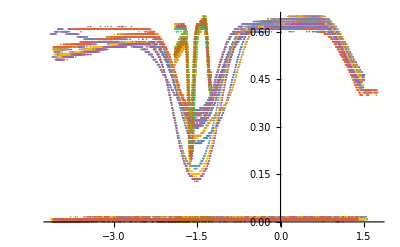

```mathematica
ListPlot3D[Table[data4[[i]],{i,1,Length[data4]}]]
```

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
data2=Table[cutoff[data1[[i]]],{i,1,Length[data1]}];
data3=Table[{data2[[i,3]],GF[data2[[i,4]],1]},{i,1,Length[data2]}];
data4=Table[xaxisD1[data3[[i]]],{i,1,Length[data3]}];
data5=Flatten[{Table[SP[data4[[i]],data4[[13+i]]],{i,1,13}],Take[data4,{27,39}]},1];
data6=Table[Transpose[{data5[[i,All,1]],GF[data5[[i,All,2]],13]}],{i,1,Length[data5]}];
```

$Aborted

$Aborted

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

$Aborted

Result

```mathematica
data10m=data4;
```

```mathematica
Manipulate[
GraphicsRow[{ListPlot[data10m[[i]],options],ListPlot[data10m[[13+i]],options]}]
,{i,1,13,1}]
```

## 20mW

Import Data

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\Plasmonics With 4WM Lab Books\\Lab Book 4 (April 16 -)\\16-9-26\\Testing EIT\\Pump 20mW"]
name=FileNames["*.csv"];
order=Ordering[StringSplit[#,"-"]&/@name];
name=name[[order]];
```

C:\Users\Admin\Qsync\QOLab\Data\Plasmonics With 4WM Lab Books\Lab Book 4 (April 16 -)\16-9-26\Testing EIT\Pump 20mW

```mathematica
name
```

{Prob-0-0.021-1.515-57.895-Sep16-.csv,Prob-0-0.021-1.5155-58.1844-Sep16-.csv,Prob-0-0.021-1.516-57.3553-Sep16-.csv,Prob-0-0.021-1.5165-58.7165-Sep16-.csv,Prob-0-0.021-1.517-58.7165-Sep16-.csv,Prob-0-0.021-1.5173-58.6338-Sep16-.csv,Prob-0-0.021-1.5176-59.1627-Sep16-.csv,Prob-0-0.021-1.5179-58.1024-Sep16-.csv,Prob-0-0.021-1.5182-59.0796-Sep16-.csv,Prob-0-0.021-1.5185-59.5218-Sep16-.csv,Prob-0-0.021-1.5188-59.4385-Sep16-.csv,Prob-0-0.021-1.5191-59.6053-Sep16-.csv,Prob-0-0.021-1.5194-59.4385-Sep16-.csv,Prob-0-0.021-1.5197-59.8769-Sep16-.csv,Scatter Pump-0-0.021-1.515-57.3553-Sep16-.csv,Scatter Pump-0-0.021-1.5155-57.7311-Sep16-.csv,Scatter Pump-0-0.021-1.516-57.895-Sep16-.csv,Scatter Pump-0-0.021-1.5165-58.7165-Sep16-.csv,Scatter Pump-0-0.021-1.517-58.7165-Sep16-.csv,Scatter Pump-0-0.021-1.5173-58.7165-Sep16-.csv,Scatter Pump-0-0.021-1.5176-59.1627-Sep16-.csv,Scatter Pump-0-0.021-1.5179-59.5218-Sep16-.csv,Scatter Pump-0-0.021-1.5182-59.5218-Sep16-.csv,Scatter Pump-0-0.021-1.5185-59.0796-Sep16-.csv,Scatter Pump-0-0.021-1.5188-59.3556-Sep16-.csv,Scatter Pump-0-0.021-1.5191-59.8769-Sep16-.csv,Scatter Pump-0-0.021-1.5194-60.3118-Sep16-.csv,Scatter Pump-0-0.021-1.5197-59.8957-Sep16-.csv,Spectrum-0-0.021-1.515-57.437-Sep16-.csv,Spectrum-0-0.021-1.5155-57.8129-Sep16-.csv,Spectrum-0-0.021-1.516-58.3491-Sep16-.csv,Spectrum-0-0.021-1.5165-58.7165-Sep16-.csv,Spectrum-0-0.021-1.517-58.6338-Sep16-.csv,Spectrum-0-0.021-1.5173-58.6338-Sep16-.csv,Spectrum-0-0.021-1.5176-59.0796-Sep16-.csv,Spectrum-0-0.021-1.5179-59.0796-Sep16-.csv,Spectrum-0-0.021-1.5182-59.5218-Sep16-.csv,Spectrum-0-0.021-1.5185-59.9605-Sep16-.csv,Spectrum-0-0.021-1.5188-59.0796-Sep16-.csv,Spectrum-0-0.021-1.5191-59.5218-Sep16-.csv,Spectrum-0-0.021-1.5194-59.9605-Sep16-.csv,Spectrum-0-0.021-1.5197-60.3959-Sep16-.csv}

```mathematica
data=Import[#]&/@name;
data1=data[[All,{1,2,3,4,5}]];
data2=Table[cutoff[data1[[i]]],{i,1,Length[data1]}];
data3=Table[{data2[[i,3]],GF[data2[[i,4]],1]},{i,1,Length[data2 ]}];
data4=Table[xaxisD[data3[[i]],600],{i,1,Length[data3]}];
data5=Flatten[{Table[SP[data4[[i]],data4[[14+i]]],{i,1,14}],Take[data4,{29,42}]},1];
data6=Table[Transpose[{data5[[i,All,1]],GF[data5[[i,All,2]],7]}],{i,1,Length[data5]}];
```

TimeSeries::mltpth: 757 paths were provided. A single path is expected.

Part::partd: Part specification … is longer than depth of object.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

TimeSeries::mltpth: 778 paths were provided. A single path is expected.

TimeSeries::mltpth: 839 paths were provided. A single path is expected.

General::stop: Further output of TimeSeries::mltpth will be suppressed during this calculation.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of … cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Transpose::argt will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

$Aborted

$Aborted

Result

```mathematica
data20m=data6;
```

```mathematica
Manipulate[
GraphicsRow[{ListPlot[data20m[[i]],options],ListPlot[data20m[[14+i]],options]}]
,{i,1,14,1}]
```

ListPlot::lpn: Transpose[{Transpose[],{}}] is not a list of numbers or pairs of numbers.

Part::partd: Part specification data20m⟦1⟧ is longer than depth of object.

ListPlot::lpn: data20m⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification data20m⟦15⟧ is longer than depth of object.

ListPlot::lpn: data20m⟦15⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification data20m⟦1⟧ is longer than depth of object.

ListPlot::lpn: data20m⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification data20m⟦15⟧ is longer than depth of object.

ListPlot::lpn: data20m⟦15⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification data20m⟦1⟧ is longer than depth of object.

ListPlot::nonopt: Options expected (instead of options) beyond position 1 in ListPlot[data20m⟦1⟧,options]. An option must be a rule or a list of rules.

Part::partd: Part specification data20m⟦15⟧ is longer than depth of object.

ListPlot::nonopt: Options expected (instead of options) beyond position 1 in ListPlot[data20m⟦15⟧,options]. An option must be a rule or a list of rules.

Part::partd: Part specification data20m⟦1⟧ is longer than depth of object.

ListPlot::lpn: data20m⟦1⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification data20m⟦15⟧ is longer than depth of object.

ListPlot::lpn: data20m⟦15⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.